```mathematica
SetDirectory[NotebookDirectory[]];
lSize={2,1,6,2};
yTicks={{1,"A"},{2,"B"},{3,"C"},{4,"D"}};
xTicks=Table[{-10i,10i},{i,1,10,1}];
```

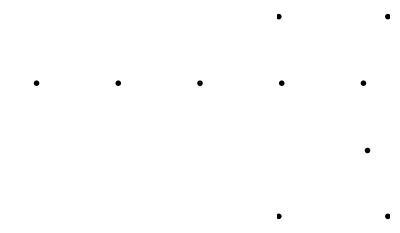

```mathematica
gOther=BarChart[lSize,BarOrigin->Right,BarOrigin->Right,ChartElements->aFish,BarSpacing->1,Frame->{True,False,False,True},FrameTicks->{xTicks,yTicks},FrameLabel->{"lake","total fish"},BaseStyle->{FontSize->Medium}]
```

```mathematica
Export["metropolisHastings_totalFish.pdf",gOther]
```

metropolisHastings_totalFish.pdf